Danial Ludwig
University of Maryland
9/6/2019

Substitution Tilings Package Tutorial

The purpose of this notebook is to convey the general usage/scope of the functions in this “Substitution Tilings Package”. Selecting Evaluation->Evaluate Notebook before starting would probably work the best.

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Substitution Tilings Package.m"
```

Graphics

Using the generateTri function allows you to skip the hassle of doing your own calculations to construct triangles:

```mathematica
myTri=generateTri[{{1,1,3},"CCW"}]
```

{{0.5,0.363271},{0.,0.},{1.,0.},{3,1,1}}

The split function, though not truly needed by the user, is the basis of the sub function. It splits the input triangle into two internal triangles based on the input vertex number and bisecting amount. Of course, the draw function is needed to see what’s actually going on:

{{{0.381966,-1.66533×10^-16},{0.5,0.363271},{0.,0.},{3,1,1}},{{0.5,0.363271},{0.381966,-1.66533×10^-16},{1.,0.},{2,2,1}}}

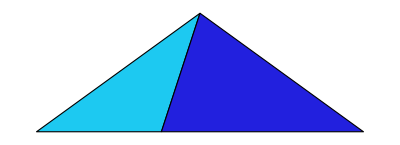

```mathematica
split[myTri,{1,1}]
draw[%]
```

The draw function generates a random color for each distinct triangle type (for the given base unit π/p, which is implied by the input triangles) every time it is called. To retain continuity, however, you can optionally input your own color association, as well as change the edge color and size. Note that it has to be of the right length, so often times the getAllTriTypes function is useful:

```mathematica
getAllTriTypes[5]
```

{{{3,1,1},CCW},{{2,2,1},CCW}}

Thus we only need to include two elements in our color association:

{{{0.381966,-1.66533×10^-16},{0.5,0.363271},{0.,0.},{3,1,1}},{{0.5,0.363271},{0.381966,-1.66533×10^-16},{1.,0.},{2,2,1}}}

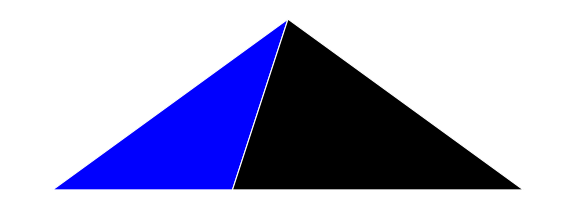

```mathematica
myColors={{{3,1,1},"CCW"}->Blue,{{2,2,1},"CCW"}->Black};
split[myTri,{1,1}]
draw[%,ColorsAssoc->myColors,EdgeClr->White,Size->Large]
```

The second argument of split is the “splitRule”, the first element telling which vertex to bisect, and the second by how many multiples of π/p. Changing the bisecting amount from 1 to 2 in myTri gives the reflected image in this case:

{{{0.618034,-2.22045×10^-16},{0.5,0.363271},{0.,0.},{2,2,1}},{{0.618034,-2.22045×10^-16},{1.,0.},{0.5,0.363271},{3,1,1}}}

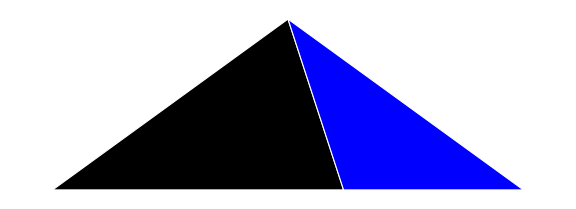

```mathematica
split[myTri,{1,2}]
draw[%,ColorsAssoc->myColors,EdgeClr->White,Size->Large]
```

The sub function takes in a “subRule”, which consists of a splitRule like above but also the specific triangle type to apply it to. Let’s keep the above 2-element list of triangles and apply the following substitution rule:

{{{0.618034,-2.22045×10^-16},{0.5,0.363271},{0.,0.},{2,2,1}},{{0.809017,0.138757},{0.618034,-2.22045×10^-16},{1.,0.},{3,1,1}},{{0.618034,-2.22045×10^-16},{0.809017,0.138757},{0.5,0.363271},{2,2,1}}}

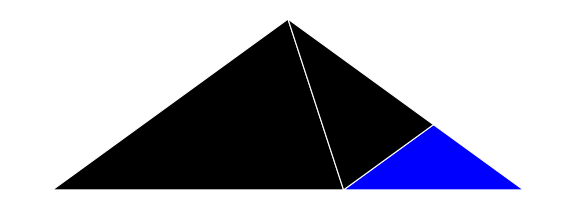

```mathematica
myTris=split[myTri,{1,2}];
mySubRule={{{3,1,1},"CCW"},{1,1}};
sub[myTris,mySubRule]
draw[%,ColorsAssoc->myColors,EdgeClr->White,Size->Large]
```

Note that only the obtuse {3,1,1} triangle was split. If we change the triType in mySubRule, obviously this will change:

{{{0.5,0.363271},{0.309017,0.224514},{0.618034,-2.22045×10^-16},{2,2,1}},{{0.309017,0.224514},{0.,0.},{0.618034,-2.22045×10^-16},{3,1,1}},{{0.618034,-2.22045×10^-16},{1.,0.},{0.5,0.363271},{3,1,1}}}

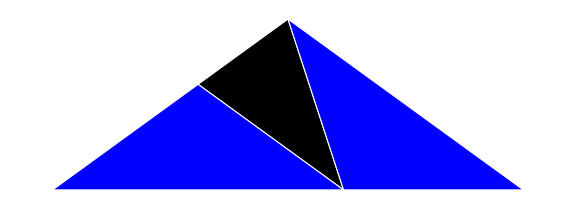

```mathematica
mySubRule={{{2,2,1},"CCW"},{1,1}};
sub[myTris,mySubRule]
draw[%,ColorsAssoc->myColors,EdgeClr->White,Size->Large]
```

So far we’ve only dealt with isosceles triangles, as those are the only two distinct triTypes with base unit π/5. π/6 introduces scalene triangles, so the second argument in triType will finally matter. Note that the following two triangles are not “reachable” by rotation:

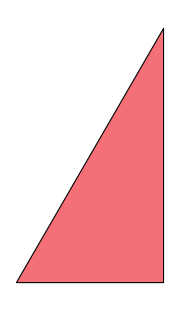
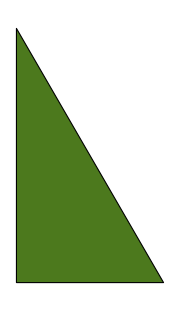

```mathematica
Row[{draw[generateTri@{{2,3,1},"CCW"},Size->Small],draw[generateTri@{{2,3,1},"CW"},Size->Small]}]
```

The triangle on the left has vertices ordered counterclockwise (denoted CCW above) when its angles are ordered from greatest to least, as opposed to the clockwise (CW) ordering of the one on the right. The sub function therefore treats them differently, as does the draw function by giving them different colors.

The randomSub function is the most important graphics function, as it applies these substitution rules a given number of times. Run it a couple times to see:

{{{0.336881,0.138757},{0.427051,0.138757},{0.309017,0.224514},{3,1,1}},{{0.427051,0.138757},{0.336881,0.138757},{0.381966,-1.66533×10^-16},{2,2,1}},{{0.454915,0.224514},{0.381966,0.277515},{0.427051,0.138757},{3,1,1}},{{0.381966,0.277515},{0.454915,0.224514},{0.5,0.363271},{2,2,1}},{{0.354102,0.191758},{0.399187,0.224514},{0.309017,0.224514},{3,1,1}},{{0.399187,0.224514},{0.354102,0.191758},{0.427051,0.138757},{2,2,1}},{{0.399187,0.224514},{0.381966,0.277515},{0.309017,0.224514},{2,2,1}},{{0.263932,0.0857567},{0.190983,0.138757},{0.236068,-2.22045×10^-16},{3,1,1}},{{0.190983,0.138757},{0.263932,0.0857567},{0.309017,0.224514},{2,2,1}},{{0.118034,0.0857567},{0.145898,-1.66533×10^-16},{0.190983,0.138757},{3,1,1}},{{0.145898,-1.66533×10^-16},{0.118034,0.0857567},{0.,0.},{2,2,1}},{{0.218847,0.0530006},{0.163119,0.0530006},{0.236068,-2.22045×10^-16},{3,1,1}},{{0.163119,0.0530006},{0.218847,0.0530006},{0.190983,0.138757},{2,2,1}},{{0.163119,0.0530006},{0.145898,-1.66533×10^-16},{0.236068,-2.22045×10^-16},{2,2,1}},{{0.354102,0.0857567},{0.263932,0.0857567},{0.381966,-1.66533×10^-16},{3,1,1}},{{0.263932,0.0857567},{0.354102,0.0857567},{0.309017,0.224514},{2,2,1}},{{0.291796,-2.63678×10^-16},{0.309017,0.0530006},{0.236068,-2.22045×10^-16},{3,1,1}},{{0.309017,0.0530006},{0.291796,-2.63678×10^-16},{0.381966,-1.66533×10^-16},{2,2,1}},{{0.309017,0.0530006},{0.263932,0.0857567},{0.236068,-2.22045×10^-16},{2,2,1}},{{0.5,0.0857567},{0.572949,0.138757},{0.427051,0.138757},{3,1,1}},{{0.572949,0.138757},{0.5,0.0857567},{0.618034,-2.22045×10^-16},{2,2,1}},{{0.545085,0.224514},{0.454915,0.224514},{0.572949,0.138757},{3,1,1}},{{0.454915,0.224514},{0.545085,0.224514},{0.5,0.363271},{2,2,1}},{{0.482779,0.138757},{0.5,0.191758},{0.427051,0.138757},{3,1,1}},{{0.5,0.191758},{0.482779,0.138757},{0.572949,0.138757},{2,2,1}},{{0.5,0.191758},{0.454915,0.224514},{0.427051,0.138757},{2,2,1}},{{0.472136,-6.10623×10^-16},{0.5,0.0857567},{0.381966,-1.66533×10^-16},{3,1,1}},{{0.5,0.0857567},{0.472136,-6.10623×10^-16},{0.618034,-2.22045×10^-16},{2,2,1}},{{0.40983,0.0857567},{0.454915,0.0530006},{0.427051,0.138757},{3,1,1}},{{0.454915,0.0530006},{0.40983,0.0857567},{0.381966,-1.66533×10^-16},{2,2,1}},{{0.454915,0.0530006},{0.5,0.0857567},{0.427051,0.138757},{2,2,1}},{{0.736068,0.0857567},{0.763932,-6.93889×10^-16},{0.809017,0.138757},{3,1,1}},{{0.763932,-6.93889×10^-16},{0.736068,0.0857567},{0.618034,-2.22045×10^-16},{2,2,1}},{{0.854102,-3.46945×10^-16},{0.881966,0.0857567},{0.763932,-6.93889×10^-16},{3,1,1}},{{0.881966,0.0857567},{0.854102,-3.46945×10^-16},{1.,0.},{2,2,1}},{{0.791796,0.0857567},{0.836881,0.0530006},{0.809017,0.138757},{3,1,1}},{{0.836881,0.0530006},{0.791796,0.0857567},{0.763932,-6.93889×10^-16},{2,2,1}},{{0.836881,0.0530006},{0.881966,0.0857567},{0.809017,0.138757},{2,2,1}},{{0.663119,0.138757},{0.690983,0.224514},{0.572949,0.138757},{3,1,1}},{{0.690983,0.224514},{0.663119,0.138757},{0.809017,0.138757},{2,2,1}},{{0.618034,0.277515},{0.545085,0.224514},{0.690983,0.224514},{3,1,1}},{{0.545085,0.224514},{0.618034,0.277515},{0.5,0.363271},{2,2,1}},{{0.618034,0.171513},{0.600813,0.224514},{0.572949,0.138757},{3,1,1}},{{0.600813,0.224514},{0.618034,0.171513},{0.690983,0.224514},{2,2,1}},{{0.600813,0.224514},{0.545085,0.224514},{0.572949,0.138757},{2,2,1}},{{0.690983,0.0530006},{0.663119,0.138757},{0.618034,-2.22045×10^-16},{3,1,1}},{{0.663119,0.138757},{0.690983,0.0530006},{0.809017,0.138757},{2,2,1}},{{0.59017,0.0857567},{0.645898,0.0857567},{0.572949,0.138757},{3,1,1}},{{0.645898,0.0857567},{0.59017,0.0857567},{0.618034,-2.22045×10^-16},{2,2,1}},{{0.645898,0.0857567},{0.663119,0.138757},{0.572949,0.138757},{2,2,1}}}

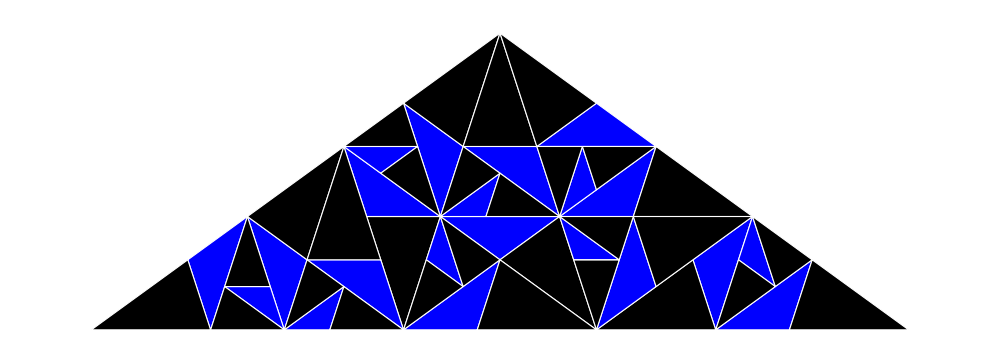

```mathematica
randomSub[myTri,10]
draw[%,ColorsAssoc->myColors,EdgeClr->White,Size->1000]
```

We’ll suppress the output from the randomSub function from here on out, but it’s good to see it at least once. Next up: adding weights to each possible substitution rule through the ProbVector option. To construct your probability vector, the best first step is to run the getAllSubRules function for the specific p-family you’re working in:

```mathematica
getAllSubRules[5]
```

{{{{3,1,1},CCW},{1,1}},{{{3,1,1},CCW},{1,2}},{{{2,2,1},CCW},{1,1}},{{{2,2,1},CCW},{2,1}}}

Thus we only need a 4-element probability vector (1 for each possible rule) like the one below:

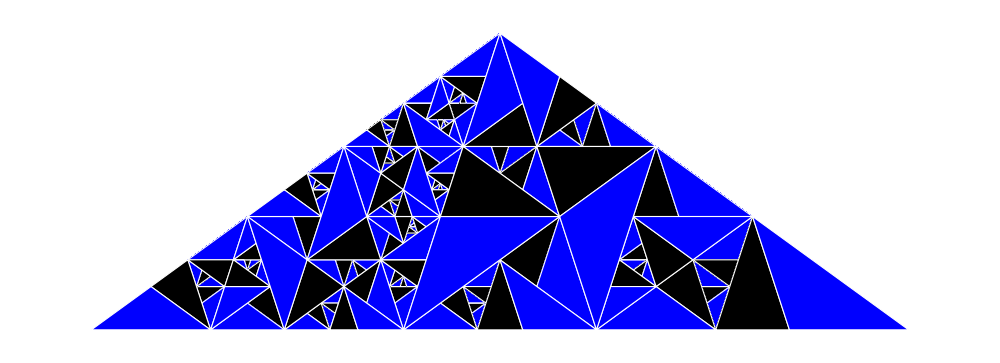

```mathematica
myProbVector={0.8,0.1,0.1,0};
randomSub[myTri,12,ProbVector->myProbVector];
draw[%,ColorsAssoc->myColors,EdgeClr->White,Size->1000]
```

Because the substitution rules on the {3,1,1} triangles were much more likely, the {2,2,1} triangles are more likely to be both larger and more common than the {3,1,1} ones.

If we increase the number of substitutions we want, it may start taking a while, so the ParallelizeQ option is there to speed it up if need be:

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

{7.99897,{{{0.454915,0.184025},{0.45898,0.171513},{0.465558,0.191758},{3,1,1}},8728,{{0.635255,0.143536},{0.645898,0.151269},{0.624612,0.151269},{3,1,1}}}}
 |  |  |  |

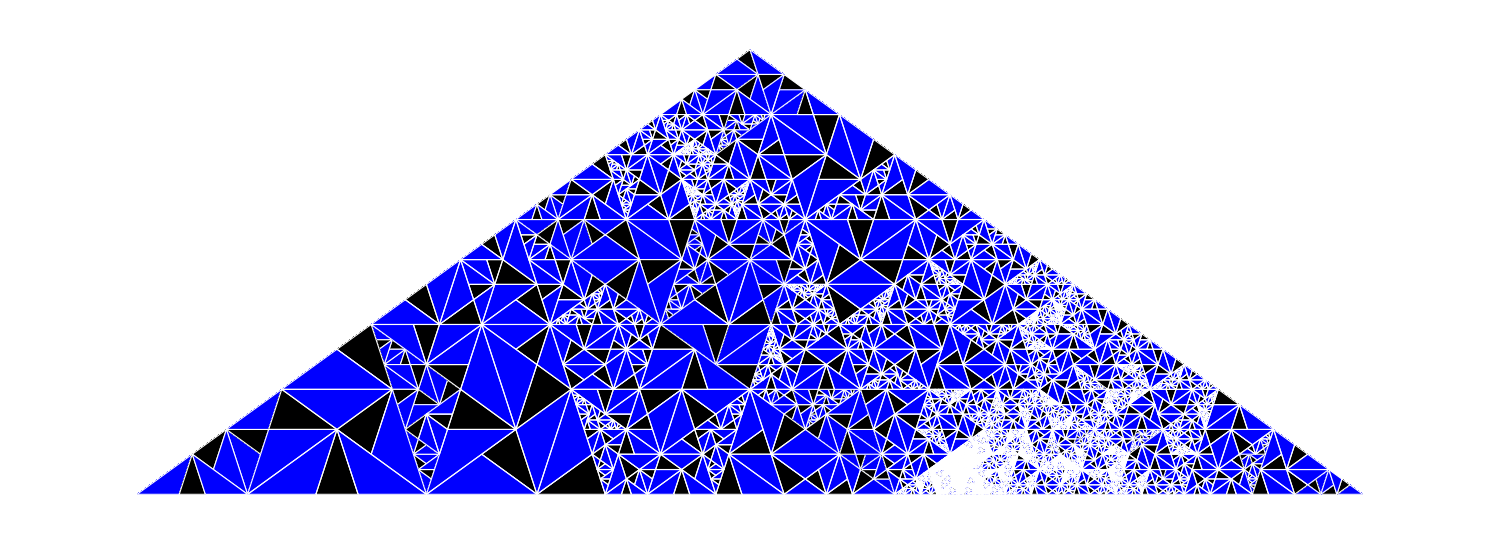

```mathematica
randomSub[myTri,25,ParallelizeQ->True]//AbsoluteTiming
draw[%[[2]],ColorsAssoc->myColors,EdgeClr->White,Size->1500]
```

In addition to just making cool pictures, these substitution tilings graphics work well with relatively Mathematica’s accessible dynamic content:

```mathematica
tropicalColors={{{3,1,1},"CCW"}->RGBColor[0.2,0.5,0.5],{{2,2,1},"CCW"}-> RGBColor[0.84,0.64,0.84]}
```

{{{3,1,1},CCW}→RGBColor[0.2, 0.5, 0.5],{{2,2,1},CCW}→RGBColor[0.84, 0.64, 0.84]}

```mathematica
penny={{-1/5,0},{1/5,0},{0,(1/5) Tan[Pi/5]},{1,1,3}};
penroses=NestList[sub[sub[#,{{{3,1,1},"CCW"},{1,1}}],{{{2,2,1},"CCW"},{2,1}}]&,penny,9];
size=5;
Manipulate[
Show[
draw[penroses[[i]],ColorsAssoc->tropicalColors,EdgeClr->Black],
PlotRange->{{-5,5}/1.6^i,{0,5}/1.6^i},ImageSize->700]
,{{i,1,"Number of Substitutions"},1,9,1}]
```

Unlike the above Manipulate, this next one is completely different each time--different p-family, different triangles, different substitutions, etc.

```mathematica
p=RandomInteger[{5,9}];
allTriTypes=getAllTriTypes@p;
startingTri=generateTri@RandomChoice@allTriTypes;
randColors=Map[#-> RGBColor[RandomReal[],RandomReal[],RandomReal[]]&,allTriTypes]

iterates=NestList[randomSub[#,1]&,startingTri,4 p];
Manipulate[
draw[iterates[[i]],Size->500,ColorsAssoc-> randColors],
{{i,1,"Number of Substitutions"},1,4 p,1}]
```

{{{3,1,1},CCW}→RGBColor[0.703512818912108, 0.4200236624317526, 0.5673075316081762],{{2,2,1},CCW}→RGBColor[0.0025839406981686963, 0.7568890860052653, 0.15812475718661623]}

Computation

Every substitution rule can be represented by a directed graph, with the vertices being all the distinct rotations of each of the distinct triangle types for a given p. The toGraph function takes in a subRule and outputs this graph:

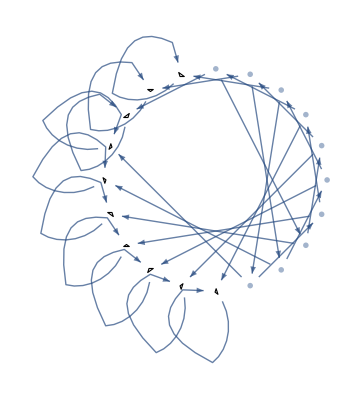

```mathematica
toGraph[{{{2,2,1},"CCW"},{1,1}},GraphObject->True]
```

Mathematica  has a lot of in-built functionality that work on graph objects, but if the adjacency matrix is all that’s needed, the GraphObject option can be left to its default value of False:

```mathematica
toGraph[{{{2,2,1},"CCW"},{1,1}}]
MatrixForm@Normal@%
```

SparseArray[…]

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

The getAllAdjMatrices function is a convenient way of getting the adjacency matrices for every possible subRule for a given p, output as a 3-D list i.e. a list of matrices. The SparseQ option allows you to use choose whether you want Normal or Sparse matrices, and the ParallelizeQ option serves the same purpose as before:

```mathematica
getAllAdjMatrices[5]
myMatrices=getAllAdjMatrices[5,SparseQ-> False]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

{{{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}},{{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}},{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.}},{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.}}}

The getLiapunovSpectrum numerically approximates the Liapunov Exponents for a given set of matrices and probability vector with n matrix multiplications.

```mathematica
getLiapunovSpectrum[myMatrices,{0.1,0.1,0.2,0.6},10000]
```

{2.,0.977816,0.977782,0.733093,0.732735,0.510058,0.502933,0.502899,0.427816,0.427458,-0.427458,-0.427816,-0.502899,-0.502933,-0.510058,-0.732735,-0.733093,-0.977782,-0.977816,-2.}

The following example assigns the {3,1,1},CCW,{1,1,} substitution a probability p and the {2,2,1},CCW,{1,1} substitution 1 - p:

```mathematica
mySpectra=Table[getLiapunovSpectrum[myMatrices,{1-p,0,p,0},10000],{p,0,1,0.01}];
```

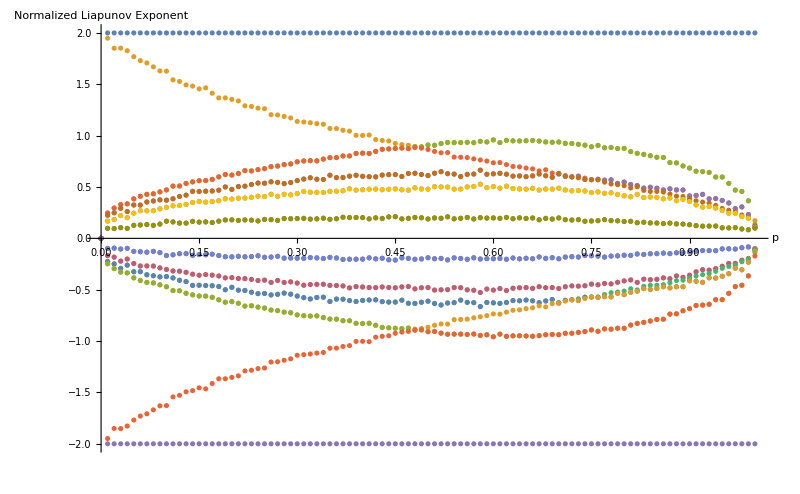

```mathematica
ListPlot[Transpose@mySpectra,DataRange->{0,1},ImageSize->800,AxesLabel->{"p","Normalized Liapunov Exponent"}]
```

For large computations, Mathematica’s speed may lag behind other languages’, so the exportAllAdjMatrices function gives an easy way of outsourcing by exporting each individual adjacency matrix as a .dat file in your notebook’s local directory. It also has a ParallelizeQ option, which is helpful for larger p-families. Un-comment and run the following cell if you want to see (and spam your folder):

```mathematica
(*
exportAllAdjMatrices@7
*)
```